```mathematica
l = 0.99 * {0.45, 0.2, 0.1, 0.25, 0.15}
op = {200*10^5, 700*10^5, 900 * 10^5, 500*10^5, 900*10^5}
q = 10^-10
```

{0.4455,0.198,0.099,0.2475,0.1485}

{20000000,70000000,90000000,50000000,90000000}

1/10000000000

```mathematica
getQ[oper_, cpuSpeed_] := oper/cpuSpeed
getP[l_, q_] := l * q
getM[qt_, q_] := qt / q
getWi[cpu_, op_, l_, q_] :=  getM[getQ[op, cpu], q] * q * getP[l, getQ[op, cpu]] / (1 - getP[l, getQ[op, cpu]])
getUi[cpu_, op_,  w_] := w + getQ[op, cpu]
```

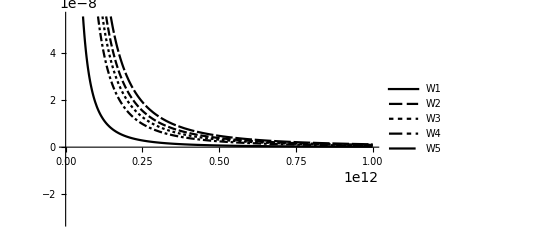

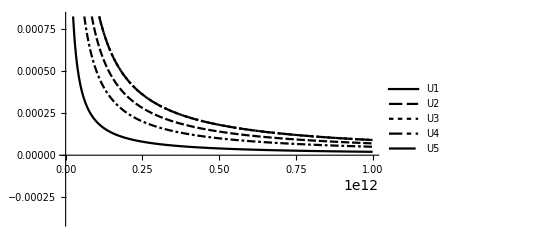

```mathematica
Plot[{getWi[cpu,op[[1]],l[[1]], q], getWi[cpu,op[[2]],l[[2]], q], getWi[cpu,op[[3]],l[[3]], q], getWi[cpu,op[[4]],l[[4]], q], getWi[cpu,op[[5]],l[[5]], q]},{cpu,10^5,10^12},PlotTheme->"Monochrome", PlotLegends->{W1,W2,W3,W4,W5}]
Plot[{getUi[cpu, op[[1]], getWi[cpu, op[[1]], l[[1]], q]], getUi[cpu, op[[2]], getWi[cpu, op[[2]], l[[2]], q]], getUi[cpu, op[[3]], getWi[cpu, op[[3]], l[[3]], q]], getUi[cpu, op[[4]], getWi[cpu, op[[4]], l[[4]], q]], getUi[cpu, op[[5]], getWi[cpu, op[[5]], l[[5]], q]]}, {cpu,10^5,10^12},PlotTheme->"Monochrome", PlotLegends->{U1,U2,U3,U4,U5}]
```